```mathematica
(*Assorted graphics commands.*)
linelegs[label_,legs_,pos_,cols_]:=PlotLegends->Placed[LineLegend[Table[Text[Style[legs[[i]],14,FontFamily->"Times New Roman"]],{i,1,Length[legs]}],LegendLabel->Text[Style[label,14,FontFamily->"Times New Roman"]],LabelStyle->{GrayLevel[0],14},LegendLayout->{"Column",cols}],pos]
frameStyle[xlabel_,ylabel_,fsize_:14]:={Axes->None,Frame->True,FrameStyle->Black,AspectRatio->1/GoldenRatio, FrameLabel->{{Text[Style[ylabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}, {Text[Style[xlabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}},LabelStyle->{FontFamily->"Times New Roman",fsize}}
text[x0_,y0_,txt_,color_]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",14],{x0,y0}]]
text[x0_,y0_,txt_,color_,size_:fontSize]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",size],{x0,y0}],Method->{"ShrinkWrap"->True}];
Cell[StyleData["Print"],FontSize->36];
frameStyle0[xlabel_,ylabel_,fsize_:14]:={Axes->None,Frame->False,AspectRatio->1/GoldenRatio, FrameLabel->{{Text[Style[ylabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}, {Text[Style[xlabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}},LabelStyle->{FontFamily->"Times New Roman",fsize}}

ResourceFunction["MaTeXInstall"][]
<<MaTeX`
```

Paclet[MaTeX,1.7.9,<>]

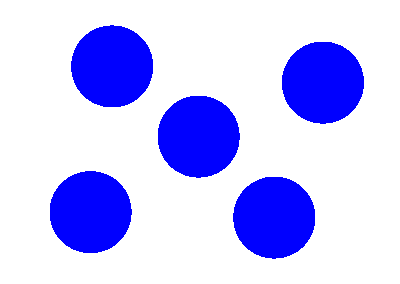

```mathematica
gradDisk//ClearAll;
gradDisk[ctr_,rad_,cf_,meshOpts:OptionsPattern@DiscretizeRegion]:=With[{reg=DiscretizeRegion[ConvexHullMesh[Table[ctr+rad {Cos[t],Sin[t]},{t,Most@Subdivide[0.,2. Pi,120]}]],meshOpts]},GraphicsComplex[MeshCoordinates[reg],MeshCells[reg,2],VertexColors->(cf/@(EuclideanDistance[ctr,#]/rad&/@MeshCoordinates[reg]))]];
blotch1=Graphics[{gradDisk[{0,0},0.75,Blend[{RGBColor[0,0,1,1],RGBColor[0,0,1,0]},#]&,MaxCellMeasure->0.01]}];
blotch2=Graphics[{gradDisk[{2.3,1},0.75,Blend[{RGBColor[0,0,1,1],RGBColor[0,0,1,0]},#]&,MaxCellMeasure->0.01]}];
blotch3=Graphics[{gradDisk[{-2,-1.4},0.75,Blend[{RGBColor[0,0,1,1],RGBColor[0,0,1,0]},#]&,MaxCellMeasure->0.01]}];
blotch4=Graphics[{gradDisk[{-1.6,1.3},0.75,Blend[{RGBColor[0,0,1,1],RGBColor[0,0,1,0]},#]&,MaxCellMeasure->0.01]}];
blotch5=Graphics[{gradDisk[{1.4,-1.5},0.75,Blend[{RGBColor[0,0,1,1],RGBColor[0,0,1,0]},#]&,MaxCellMeasure->0.01]}];
whiterect=Graphics[{White,Rectangle[{-3,-2},{3,2}]}];
Show[{whiterect,blotch1, blotch2,blotch3,blotch4,blotch5}]
```

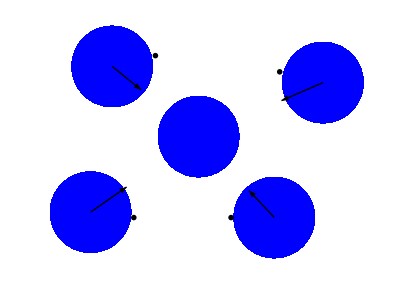
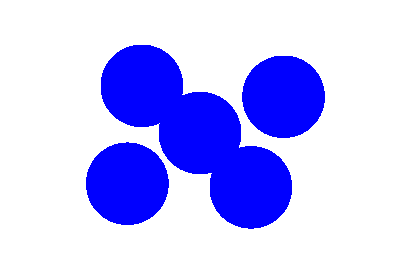
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
mult=1.5;
blotch1pert=Graphics[{gradDisk[{0,0}/mult,0.75,Blend[{RGBColor[0,0,1,1],RGBColor[0,0,1,0]},#]&,MaxCellMeasure->0.01]}];
blotch2pert=Graphics[{gradDisk[{2.3,1}/mult,0.75,Blend[{RGBColor[0,0,1,1],RGBColor[0,0,1,0]},#]&,MaxCellMeasure->0.01]}];
blotch3pert=Graphics[{gradDisk[{-2,-1.4}/mult,0.75,Blend[{RGBColor[0,0,1,1],RGBColor[0,0,1,0]},#]&,MaxCellMeasure->0.01]}];
blotch4pert=Graphics[{gradDisk[{-1.6,1.3}/mult,0.75,Blend[{RGBColor[0,0,1,1],RGBColor[0,0,1,0]},#]&,MaxCellMeasure->0.01]}];
blotch5pert=Graphics[{gradDisk[{1.4,-1.5}/mult,0.75,Blend[{RGBColor[0,0,1,1],RGBColor[0,0,1,0]},#]&,MaxCellMeasure->0.01]}];
Arrow1=Graphics[{Thick,{Arrowheads[0.05],Arrow[{{2.3,1},{2.3,1}/mult}]}}];
Arrow2=Graphics[{Thick,{Arrowheads[0.05],Arrow[{{-2,-1.4},{-2,-1.4}/mult}]}}];
Arrow3=Graphics[{Thick,{Arrowheads[0.05],Arrow[{{-1.6,1.3},{-1.6,1.3}/mult}]}}];
Arrow4=Graphics[{Thick,{Arrowheads[0.05],Arrow[{{1.4,-1.5},{1.4,-1.5}/mult}]}}];
textstuff=Graphics[MaTeX["\\delta n \\approx -n_0 \\nabla\\cdot\\mathcal{U}>0",Magnification->1.5],ImagePadding->{{0,0},{0,0}}];
text1=Graphics[Text[MaTeX["\\mathcal{U}(x_{1})",Magnification->1],{-0.8,1.5}]];
text3=Graphics[Text[MaTeX["\\mathcal{U}(x_{3})",Magnification->1],{-1.2,-1.5}]];
text2=Graphics[Text[MaTeX["\\mathcal{U}(x_{2})",Magnification->1],{1.5,1.2}]];
text4=Graphics[Text[MaTeX["\\mathcal{U}(x_{4})",Magnification->1],{0.6,-1.5}]];
Grid[{{textstuff,SpanFromLeft},{Show[{whiterect,blotch1, blotch2,blotch3,blotch4,blotch5,Arrow1,Arrow2,Arrow3,Arrow4,text1,text2,text3,text4}],Show[{whiterect,blotch1pert, blotch2pert,blotch3pert,blotch4pert,blotch5pert}]}},Spacings->{0,0},Frame->{All,All}]
```